{1,0.618,0.414,0.295,0.22,0.169}

{-1,-0.618,-0.414,-0.295,-0.22,-0.169}

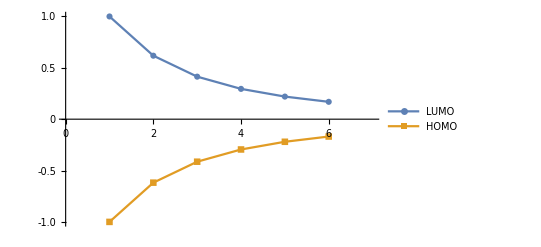

```mathematica
Get["MaTeX`"]
a={1,0.618,0.414,0.295,0.220,0.169}
b={-1,-0.618,-0.414,-0.295,-0.220,-0.169}

ListLinePlot[{a,b},
PlotMarkers->Automatic,
PlotRange->{{0,7},Automatic},
Ticks->{Table[{i,i},{i,0,7}],All},
PlotLegends->{LUMO,HOMO},
AxesLabel->{MaTeX["N"],MaTeX["E=\alpha+k\\beta"]},
LabelStyle->Directive[FontFamily->"CMU Serif",FontSize->10.5]
]
```